## 13 TeV with PDF Monolepton

### Load Parton Level (dσ̂/d Cθ)

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

(* Load dσ/dΩ *)

dσhatdCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-udbar2lpv_X-sec.txt"]]
```

(80698.2 Ein^2 ((-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^4 (0.0816212 x^2 (CHD28til-CHD8til+6 δGF6^2-4 √2 δGF8)-0.461719 δGF6 x+0.65297)^4 (Cθ^2 (4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2+CHud6til^2 x^2+4)+2 Cθ (4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2-CHud6til^2 x^2+4)+4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2+CHud6til^2 x^2+4)+4 (Cθ+1)^2 CLQ36til^2 x^2 (6462.07 (0.511403 x^2 (1. CHD28til-1. CHD8til+1.33333 CHL36til^2-3.77124 CHL36til δGF6+1.33333 CHL38til+2.66667 CHQ36til^2-7.54247 CHQ36til δGF6+2.66667 CHQ38til+0.666667 CHud6til^2+8. δGF6^2-5.65685 δGF8)+1.36374 x (1. CHL36til+2. CHQ36til-2.12132 δGF6)+2.04561)^2+16 Ein^4-51696.6 Ein^2+4.17583×10^7)+2 (Cθ+1)^2 (4 Ein^2-6462.07) x (0.0816212 x^2 (CHD28til-CHD8til+6 δGF6^2-4 √2 δGF8)-0.461719 δGF6 x+0.65297)^2 (4 CLQ36til (CHL36til x+CHQ36til x+1) (-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^2+x ((2 CHLQ28til+CHLQ58til) (-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^2-8 CLQs38til Ein^2-4 (Cθ-1) CLQt38til Ein^2))))/((-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^4 (6462.07 (0.511403 x^2 (1. CHD28til-1. CHD8til+1.33333 CHL36til^2-3.77124 CHL36til δGF6+1.33333 CHL38til+2.66667 CHQ36til^2-7.54247 CHQ36til δGF6+2.66667 CHQ38til+0.666667 CHud6til^2+8. δGF6^2-5.65685 δGF8)+1.36374 x (1. CHL36til+2. CHQ36til-2.12132 δGF6)+2.04561)^2+16 Ein^4-51696.6 Ein^2+4.17583×10^7))

### PDF Convolution (Only do Once!)

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{12.7336,Null}

```mathematica
?xPDFcv
```

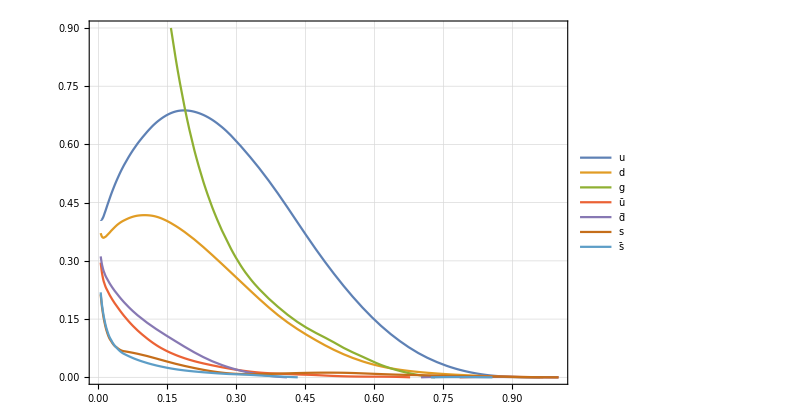

```mathematica
(* Plot xPDF : Peskin pg 563 *)
uppdf=xPDFcv[x,4,2];  (* Peak height is different from the Peskin *)
downpdf=xPDFcv[x,4,1];
gluepdf=xPDFcv[x,4,0];
upbarpdf=xPDFcv[x,4,-2];
dbarpdf=xPDFcv[x,4,-1];
spdf=xPDFcv[x,4,3];
sbarpdf=xPDFcv[x,4,-3];   
Plot[{uppdf,downpdf,gluepdf,upbarpdf,dbarpdf,spdf,sbarpdf},{x,0.005,1},PlotRange->{{0,1},{0,0.9}},PlotLegends->{"u","d","g","ū","d̄","s","s̄"}]
```

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;

(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,mz^2,flav]>0,1/x xPDFcv[x,mz^2,flav],0]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

(* Parton Luminosity *)
Lq[list_,ecoll_,M1_,M2_,quarkID1_,quarkID2_]:=Block[{ArrayL1,Mcounts,Mvalue,IntL,Qgluon},
ArrayL1={};
Mcounts=300;
If[quarkID1==0 && quarkID2==0,Qgluon=-1,Qgluon=1];
Monitor[For[j=1,j≤Mcounts,j+=1,
Mvalue=(M1+(M2-M1)/(Mcounts-1)(j-1))//N;
AppendTo[ArrayL1,{Mvalue,(2Mvalue)/ecoll^2 NIntegrate[1/(x((1-Qgluon)/2+1))(pdf[x, Mvalue,quarkID1]pdf[Mvalue^2/(x ecoll^2), Mvalue,quarkID2]+pdf[x, Mvalue,quarkID2]pdf[Mvalue^2/(x ecoll^2), Mvalue,quarkID1]),{x,Mvalue^2/ecoll^2,1}]}];
(*((1-Qgluon)/2+1) for glue-glue collision*) (* 2Mvalue comes from d/dM^2 -> 1/(2M)d/dM*)

],j];
(* Interpolate *)
IntL=Interpolation[ArrayL1];
(* Output *)
If[list==1,Return[ArrayL1],Return[IntL]]
]
```

```mathematica
(* We now calculate the DATA for the Luminosity functions to be used later *)
LudbarList1=Lq[1,ecoll,1,2000,2,-1];
LudbarList2=Lq[1,ecoll,2000,4000,2,-1];
LudbarList3=Lq[1,ecoll,4000,9000,2,-1];
LudbarList4=Lq[1,ecoll,9000,13000,2,-1];
(*Export["~/Dropbox/1_Dilepton_study/Luminosity_up_list.txt",LupList];*)
(*Ludbar=Interpolation[LudbarList];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.996808}. NIntegrate obtained 1.36177×10^-16 and 1.62114×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.952274}. NIntegrate obtained 3.85252×10^-18 and 1.52705×10^-23 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
LudbarList=Join[LudbarList1,Delete[LudbarList2,{{1}}],Delete[LudbarList3,{{1}}],Delete[LudbarList4,{{1}}]];
Ludbar=Interpolation[LudbarList];
```

```mathematica
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/Luminosity_udbar_list_nlo_Adam.txt",LudbarList,"Table"];
```

### Loading Saved Parton Luminosity

```mathematica
LudbarList=Import["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/Luminosity_udbar_list_nlo_Adam.txt","Table"];
Ludbar=Interpolation[LudbarList];
```

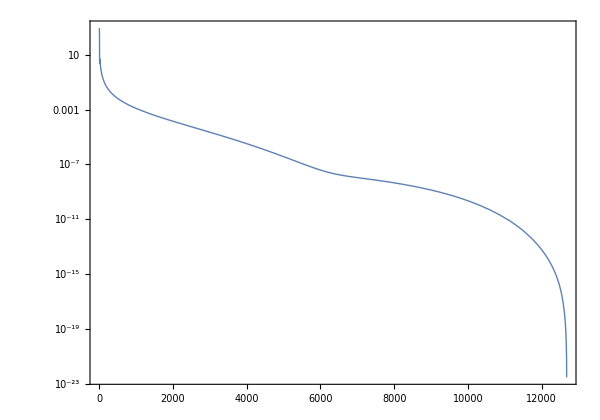

```mathematica
LogPlot[Ludbar[x],{x,1,13000},Frame->True,PlotRange->All]
```

### Assign Wilson Coefficients (Need to fix or Implement for Later)

```mathematica
(*wilsonCoeflist={};
onlySM={};
variablelist = DeleteDuplicates@Cases[dσhatdCθ,_Symbol,Infinity]
variablelist=Delete[variablelist,{{1},{12}}]

(*For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[wilsonCoeflist,variablelist[[coef]]->7*10^-5]]
For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[onlySM,variablelist[[coef]]->0.]]*)


dσdCθwil = dσhatdCθ
dσdCθSM = dσhatdCθ/.x->0*)
```

### Proton Level Calculation

#### dσ/dM Calculation

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
dσdCθwil = dσhatdCθ;
partonicσ[n_]:=Integrate[SeriesCoefficient[dσdCθwil,{x,0,n}],{Cθ,-1,1}]/.{Ein->M/2}//Simplify
```

```mathematica
variablelistOx = DeleteDuplicates@Cases[partonicσ[1],_Symbol,Infinity];
variablelistOx=Delete[variablelistOx,{{1}}]
dσdMOxterm=Table[Coefficient[partonicσ[1],variablelistOx[[wilson]]],{wilson,1,Length[variablelistOx]}]
```

{CHL36til,CHQ36til,CLQ36til,δGF6}

{(5.16469×10^6 M^2 (0.0151493 M^4-195.791 M^2+632744.))/((M^4-12924.1 M^2+4.17854×10^7)^2),(5.16469×10^6 M^2 (0.0151493 M^4-195.791 M^2+632471.))/((M^4-12924.1 M^2+4.17854×10^7)^2),(5.16469×10^6 M^2 (5.86084×10^-7 M^6-0.0113619 M^4+73.4375 M^2-158254.))/((M^4-12924.1 M^2+4.17854×10^7)^2),(5.16469×10^6 M^2 (-0.0214243 M^4+276.89 M^2-894642.))/((M^4-12924.1 M^2+4.17854×10^7)^2)}

```mathematica
variablelistOx2={CLQs38til,CHud6til^2,CHD8til,CHD28til,CHQ38til,CHL38til,CHQ36til^2,CHL36til^2,CHQ36til CHL36til,CHL36til CLQ36til,CHQ36til CLQ36til,CHLQ28til,CHLQ58til,CLQ36til^2,CLQt38til, δGF6^2,CHL36til δGF6,CHQ36til δGF6,δGF6 CLQ36til,δGF8}
dσdMOx2term=Table[Coefficient[partonicσ[2],variablelistOx2[[wilson]]],{wilson,1,Length[variablelistOx2]}]
```

{CLQs38til,CHud6til^2,CHD8til,CHD28til,CHQ38til,CHL38til,CHQ36til^2,CHL36til^2,CHL36til CHQ36til,CHL36til CLQ36til,CHQ36til CLQ36til,CHLQ28til,CHLQ58til,CLQ36til^2,CLQt38til,δGF6^2,CHL36til δGF6,CHQ36til δGF6,CLQ36til δGF6,δGF8}

{(8.2635×10^7 M^2 (-3.02109×10^-13 M^12+9.76126×10^-9 M^10-0.000126172 M^8+0.815545 M^6-2636.08 M^4+3.40867×10^6 M^2))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000118354 M^8-3.05924 M^6+29655.6 M^4-1.27776×10^8 M^2+2.06469×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (-0.000236707 M^8+6.11847 M^6-59313.4 M^4+2.5558×10^8 M^2-4.13027×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000236707 M^8-6.11847 M^6+59313.4 M^4-2.5558×10^8 M^2+4.13027×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000473414 M^8-12.2369 M^6+118622. M^4-5.11105×10^8 M^2+8.25877×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000473414 M^8-12.2369 M^6+118631. M^4-5.11215×10^8 M^2+8.26233×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000473414 M^8-12.2369 M^6+118531. M^4-5.09928×10^8 M^2+8.22075×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000473414 M^8-12.2369 M^6+118591. M^4-5.107×10^8 M^2+8.2457×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.00189366 (M^4-12924.1 M^2+4.17854×10^7)^2-125.17 (M^4-12924.1 M^2+4.17854×10^7)+2.46159×10^6))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (3.66302×10^-8 (M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)^2-0.00132068 (1. M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (3.66302×10^-8 (M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)^2-0.00264136 (1. M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (1.83151×10^-8 M^10-0.000591768 M^8+7.64908 M^6-49441.7 M^4+1.5981×10^8 M^2-2.06647×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (9.15756×10^-9 M^10-0.000295884 M^8+3.82454 M^6-24720.8 M^4+7.99049×10^7 M^2-1.03324×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (7.08562×10^-13 M^12-2.74727×10^-8 M^10+0.000443883 M^8-3.82553 M^6+18547.8 M^4-4.79678×10^7 M^2+5.16953×10^10))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (7.55273×10^-14 M^12-2.44031×10^-9 M^10+0.000031543 M^8-0.203886 M^6+659.019 M^4-852167. M^2))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.00284048 M^8-73.4216 M^6+711658. M^4-3.06564×10^9 M^2+4.95205×10^12))/((M^4-12924.1 M^2+4.17854×10^7)^3),1/((M^4-12924.1 M^2+4.17854×10^7)^3)8.2635×10^7 M^2 (6.75737×10^-19 (M^4-12924.1 M^2+4.17854×10^7)^2-0.00267803 (1. M^4-12924.1 M^2+4.17583×10^7) (M^4-12924.1 M^2+4.17854×10^7)+96.5547 (M^4-12924.1 M^2+4.17854×10^7)-2.61091×10^6),1/((M^4-12924.1 M^2+4.17854×10^7)^3)8.2635×10^7 M^2 (6.75737×10^-19 (M^4-12924.1 M^2+4.17854×10^7)^2-0.00267803 (1. M^4-12924.1 M^2+4.17583×10^7) (M^4-12924.1 M^2+4.17854×10^7)+193.109 (M^4-12924.1 M^2+4.17854×10^7)-5.22182×10^6),(8.2635×10^7 M^2 (1.03109×10^-23 (M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)^2-1.03606×10^-7 (1. M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7) (1. M^4-12924.1 M^2+4.17583×10^7)))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (-0.00133902 M^8+34.6113 M^6-335527. M^4+1.44578×10^9 M^2-2.33644×10^12))/((M^4-12924.1 M^2+4.17854×10^7)^3)}

```mathematica
1/10^5 Vegas[10^5 Ludbar[M]partonicσ[0], {M, 1, 13000},MaxPoints-> 5000000,NStart-> 100000, PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
```

Vegas::success: Needed 505000 function evaluations.

(8171.1 | 6.6962 | 4.16689×10^-10)

```mathematica
intSM=NIntegrate[Ludbar[M]partonicσ[0],{M,1,13000}]
int1=Table[NIntegrate[Ludbar[M]dσdMOxterm[[i]],{M,1,13000}],{i,1,4}]
int2=Table[NIntegrate[Ludbar[M]dσdMOx2term[[i]],{M,1,13000}],{i,1,Length[variablelistOx2]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {83.8737}. NIntegrate obtained 8186.99 and 683.274 for the integral and error estimates.

8186.99

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {83.8737}. NIntegrate obtained 10815.4 and 483.24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {83.8737}. NIntegrate obtained 5228.37 and 2319.75 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {83.8737}. NIntegrate obtained 10.4744 and 3.06279 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{10815.4,5228.37,10.4744,-11334.6}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {83.8737}. NIntegrate obtained -73.7738 and 0.122301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {83.8737}. NIntegrate obtained 653.546 and 289.969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {83.8737}. NIntegrate obtained -2003.69 and 364.775 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-73.7738,653.546,-2003.69,2003.69,2614.18,5407.71,-4056.17,-1839.81,14932.,10.6868,10.8991,5.23721,2.61861,171.996,18.4434,16536.7,-15590.9,-8519.23,-30.0766,-11334.6}

```mathematica
SeriesCoefficient[1/intSM(intSM+int1.variablelistOx x+int2.variablelistOx2 x^2),{x,0,1}]//Expand
SeriesCoefficient[1/intSM(intSM+int1.variablelistOx x+int2.variablelistOx2 x^2),{x,0,2}]//Expand
```

1.32105 CHL36til+0.638619 CHQ36til+0.0012794 CLQ36til-1.38446 δGF6

0.244741 CHD28til-0.244741 CHD8til-0.224724 CHL36til^2+1.82387 CHL36til CHQ36til+0.00130533 CHL36til CLQ36til-1.90435 CHL36til δGF6+0.660524 CHL38til+0.000639699 CHLQ28til+0.000319849 CHLQ58til-0.495441 CHQ36til^2+0.00133127 CHQ36til CLQ36til-1.04058 CHQ36til δGF6+0.319309 CHQ38til+0.0798273 CHud6til^2+0.0210084 CLQ36til^2-0.0036737 CLQ36til δGF6-0.00901109 CLQs38til+0.00225277 CLQt38til+2.01987 δGF6^2-1.38446 δGF8

```mathematica
(* Tae *){10815.4,5228.37,10.4744,-11334.6}.{c36HψL,c36Hψq,cLQ3,δGF6}
```

10815.4 c36HψL+5228.37 c36Hψq+10.4744 cLQ3-11334.6 δGF6

```mathematica
(* Adam *)11274.1 c36HψL+5617.18 c36Hψq+5.44834 cLQ3-11943.9 δGF6
```

11274.1 c36HψL+5617.18 c36Hψq+5.44834 cLQ3-11943.9 δGF6

```mathematica
(* Tae *){-73.7738,653.546,-2003.69,2003.69,2614.18,5407.71,-4056.17,-1839.81,14932.,10.6868,10.8991,5.23721,2.61861,171.996,18.4434,16536.7,-15590.9,-8519.23,-30.0766,-11334.6}.{c8LQ3s,cHud6^2,c8HD,c8HD2,c38Hψq,c38HψL,c36Hψq^2,c36HψL^2,c36Hψq c36HψL,c36HψL cLQ3,c36Hψq cLQ3,c8LQ2,c8LQ5,cLQ3^2,c8LQ3t, δGF6^2,c36HψL δGF6,c36Hψq δGF6,δGF6 cLQ3,δGF8}
```

-1839.81 c36HψL^2+14932. c36HψL c36Hψq+10.6868 c36HψL cLQ3-15590.9 c36HψL δGF6-4056.17 c36Hψq^2+10.8991 c36Hψq cLQ3-8519.23 c36Hψq δGF6+5407.71 c38HψL+2614.18 c38Hψq-2003.69 c8HD+2003.69 c8HD2+5.23721 c8LQ2-73.7738 c8LQ3s+18.4434 c8LQ3t+2.61861 c8LQ5+653.546 cHud6^2+171.996 cLQ3^2-30.0766 cLQ3 δGF6+16536.7 δGF6^2-11334.6 δGF8

```mathematica
(* Adam *)168.996 (-11.2677 c36HψL^2+88.8233 c36HψL c36Hψq+0.0372414 c36HψL cLQ3-94.0451 c36HψL δGF6-27.9816 c36Hψq^2+0.0422434 c36Hψq cLQ3-46.7388 c36Hψq δGF6+33.356 c38HψL+16.6193 c38Hψq-12.4938 c8HD+12.4938 c8HD2+0.0161197 c8LQ2-0.427227 c8LQ3s+0.106807 c8LQ3t+0.00805984 c8LQ5+4.15482 cHud6^2+1. cLQ3^2-0.101798 cLQ3 δGF6+99.7499 δGF6^2-70.6758 δGF8)//Expand
```

-1904.2 c36HψL^2+15010.8 c36HψL c36Hψq+6.29365 c36HψL cLQ3-15893.2 c36HψL δGF6-4728.78 c36Hψq^2+7.13897 c36Hψq cLQ3-7898.67 c36Hψq δGF6+5637.03 c38HψL+2808.6 c38Hψq-2111.4 c8HD+2111.4 c8HD2+2.72416 c8LQ2-72.1997 c8LQ3s+18.05 c8LQ3t+1.36208 c8LQ5+702.148 cHud6^2+168.996 cLQ3^2-17.2035 cLQ3 δGF6+16857.3 δGF6^2-11943.9 δGF8